```mathematica
"Leah Dougherty
ChE 272 Final Project
March 4, 2009
Part I"
```

```mathematica
"P CONTROL"
```

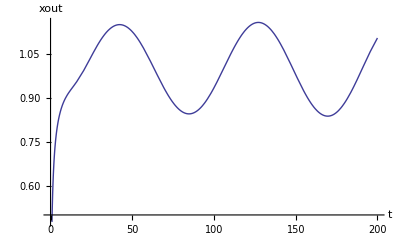

```mathematica
a=0.75;
x0=0 ;
Vin = UnitStep[0];
(*Vin=vapor in*)

k=13;
DESolve =NDSolve [{x1'[t]==k*error[t]-(1+a)*x1[t]+a*x2[t],
 x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
 x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
 x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
 x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
 x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
 x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
 x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
 x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
 x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
 x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
 x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
 x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
 x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
 x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
 x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
 x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
 x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
 x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
 x20'[t]==x19[t]-(1+a)*x20[t]+Vin, 
error[t]== Vin-x20[t],
x1[0] ==0, x2[0]==0, x3[0] ==0, x4[0]==0, x5[0]==0, x6[0] ==0, x7[0]==0, x8[0] ==0, x9[0]==0, x10[0] ==0, 
x11[0] ==0, x12[0]==0, x13[0] ==0, x14[0]==0, x15[0]==0, x16[0] ==0, x17[0]==0, x18[0] ==0, x19[0]==0, x20[0] ==0, error[0]==1}, 
{x1[t] , x2[t], x3[t], x4[t], x5[t], x6[t], x7[t], x8[t], x9[t], x10[t],
x11[t] , x12[t], x13[t], x14[t], x15[t], x16[t], x17[t], x18[t], x19[t], x20[t], error[t]},{t, 0,200}];

Plot[Evaluate[x20[t]/.DESolve], {t,0,200},AxesLabel->{"t","xout"}]
```

```mathematica
"PI CONTROL"
```

```mathematica
a=0.75;
x0=0 ;
Vin = UnitStep[0];
(*Vin=vapor in*)

kc=13;
pu=1;
tauI=pu/1.2;
kI=kc/tauI;
(*errorINT[t]=NIntegrate[error[t], {t, 0, 200}]
u[t]=kc*error[t]+kI*errorINT[t]*)


DESolve =NDSolve [{x1'[t]==u[t]-(1+a)*x1[t]+a*x2[t],
 x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
 x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
 x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
 x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
 x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
 x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
 x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
 x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
 x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
 x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
 x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
 x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
 x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
 x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
 x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
 x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
 x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
 x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
 x20'[t]==x19[t]-(1+a)*x20[t]+Vin, 
error[t]== Vin-x20[t],
errrorINT[t]==NIntegrate[error[t], {t, 0, 200}],
u[t]==kc*error[t]*kI*errorINT[t],
x1[0] ==0, x2[0]==0, x3[0] ==0, x4[0]==0, x5[0]==0, x6[0] ==0, x7[0]==0, x8[0] ==0, x9[0]==0, x10[0] ==0, 
x11[0] ==0, x12[0]==0, x13[0] ==0, x14[0]==0, x15[0]==0, x16[0] ==0, x17[0]==0, x18[0] ==0, x19[0]==0, x20[0] ==0, error[0]==1, errorINT[0]== 0, u[0]== kc}, 
{x1[t] , x2[t], x3[t], x4[t], x5[t], x6[t], x7[t], x8[t], x9[t], x10[t],
x11[t] , x12[t], x13[t], x14[t], x15[t], x16[t], x17[t], x18[t], x19[t], x20[t], error[t], errorINT[t], u[t]},{t, 0,200}]

Plot[Evaluate[x20[t]/.DESolve], {t,0,200},AxesLabel->{"t","xout"}]
```

NIntegrate::inumr: The integrand error[t] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 200}}.

NIntegrate::write: Tag Slot in #1 is Protected.

NIntegrate::itraw: Raw object 0. cannot be used as an iterator.

NDSolve::nlnum: The function value {-13., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 13 »} is not a list of numbers with dimensions {23} at {t, error[t], errorINT[t], u[t], x1[t], x10[t], x11[t], x12[t], x13[t], x14[t], « 37 »} = {0., 1., 0., 13., 0., 0., 0., 0., 0., 0., « 37 »}.

{}

-Graphics-

```mathematica
"PID CONTROL"
```

```mathematica
a=0.75;
x0=0;
Vin=UnitStep[0];
kc=0.5;
pu=1;
tauI=pu/2;
tauD=pu/8;
kI=kc/tauI;
kD=kc*tauD;

u[t]=kc*(error[t]+(1/tauI)*(∫_0^t error[σ]ⅆσ)-tauD*Dt[x20[t],t])

DESolve =NDSolve [{x1'[t]==u[t]*error[t]-(1+a)*x1[t]+a*x2[t],
 x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
 x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
 x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
 x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
 x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
 x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
 x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
 x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
 x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
 x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
 x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
 x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
 x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
 x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
 x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
 x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
 x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
 x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
 x20'[t]==x19[t]-(1+a)*x20[t]+Vin, 
error[t]== Vin-x20[t],
x1[0] ==0, x2[0]==0, x3[0] ==0, x4[0]==0, x5[0]==0, x6[0] ==0, x7[0]==0, x8[0] ==0, x9[0]==0, x10[0] ==0, 
x11[0] ==0, x12[0]==0, x13[0] ==0, x14[0]==0, x15[0]==0, x16[0] ==0, x17[0]==0, x18[0] ==0, x19[0]==0, x20[0] ==0, error[0]==1}, 
{x1[t] , x2[t], x3[t], x4[t], x5[t], x6[t], x7[t], x8[t], x9[t], x10[t],
x11[t] , x12[t], x13[t], x14[t], x15[t], x16[t], x17[t], x18[t], x19[t], x20[t], error[t]},{t, 0,200}]

Plot[Evaluate[x20[t]/.DESolve], {t,0,200},AxesLabel->{"t","xout"}]
```